```mathematica
(****************Analysis across projection types****************************)
```

```mathematica
ccColor=RGBColor["#ff1f5b"];
```

```mathematica
ctColor=Blue;
```

```mathematica
ccData={ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS4/FigureS4Data/V1CC/","Mouse23112","/","Mouse23112","_meanLaminarFluor.txt"],"List"],ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS4/FigureS4Data/V1CC/","Mouse23166","/","Mouse23166","_meanLaminarFluor.txt"],"List"],ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS4/FigureS4Data/V1CC/","Mouse23184","/","Mouse23184","_meanLaminarFluor.txt"],"List"]};
```

```mathematica
ccInterp=Interpolation/@ccData;
```

```mathematica
meanCC=Mean[Table[Table[{n,ccInterp[[m]][n]},{n,0,149,0.15}],{m,1,Length[ccInterp]}]];
```

```mathematica
semCC=StandardDeviation[Table[Table[ccInterp[[m]][n],{n,0,149,0.15}],{m,1,Length[ccInterp]}]]/Sqrt[Length[ccInterp]];
```

```mathematica
meanPlusSEMcc=Table[{meanCC[[n,1]],meanCC[[n,2]]+semCC[[n]]},{n,1,Length[meanCC]}];
```

```mathematica
meanMinusSEMcc=Table[{meanCC[[n,1]],meanCC[[n,2]]-semCC[[n]]},{n,1,Length[meanCC]}];
```

```mathematica
ctData={ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS4/FigureS4Data/V1CT/","Mouse23131","/","Mouse23131","_meanLaminarFluor.txt"],"List"],ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS4/FigureS4Data/V1CT/","Mouse23132","/","Mouse23132","_meanLaminarFluor.txt"],"List"],ToExpression/@Import[StringJoin["F:/FigureGeneration/FigureS4/FigureS4Data/V1CT/","Mouse23138","/","Mouse23138","_meanLaminarFluor.txt"],"List"]};
```

```mathematica
ctInterp=Interpolation/@ctData;
```

```mathematica
meanCT=Mean[Table[Table[{n,ctInterp[[m]][n]},{n,0,149,0.15}],{m,1,Length[ctInterp]}]];
```

```mathematica
semCT=StandardDeviation[Table[Table[ctInterp[[m]][n],{n,0,149,0.15}],{m,1,Length[ctInterp]}]]/Sqrt[Length[ctInterp]];
```

```mathematica
meanPlusSEMct=Table[{meanCT[[n,1]],meanCT[[n,2]]+semCT[[n]]},{n,1,Length[meanCT]}];
```

```mathematica
meanMinusSEMct=Table[{meanCT[[n,1]],meanCT[[n,2]]-semCT[[n]]},{n,1,Length[meanCT]}];
```

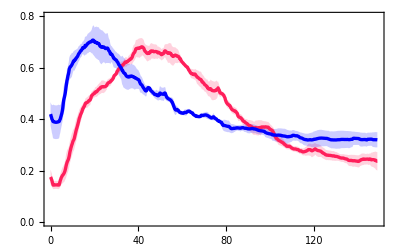

```mathematica
ListLinePlot[{meanCC,meanPlusSEMcc,meanMinusSEMcc,meanCT,meanPlusSEMct,meanMinusSEMct},Filling->{1->{{2},Directive[Opacity[0.2],ccColor]},1->{{3},Directive[Opacity[0.2],ccColor]},4->{{5},Directive[Opacity[0.2],ctColor]},4->{{6},Directive[Opacity[0.2],ctColor]}},PlotStyle->{{ccColor,Thickness[0.006]},Transparent,Transparent,{ctColor,Thickness[0.006]},Transparent,Transparent},PlotRange->{{0,149},{0,0.8}},FrameTicks->{{LinTicks[0,0.8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,149,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```